EL SIGUIENTE CÓDIGO ESTA LICENCIADO BAJO GNU GPLv3, ESTA PUEDE SER ENCONTRADA DENTRO DEL PAQUETE, COMO UN RECURSO, CON EL NOMBRE LICENSE.TXT

```mathematica
(*
Para la ejecución del algoritmo es necesario generar una lista de los polígonos que componen al grafo,una lista de los vertices de la periferia y con esta,a su vez,obtener la lista de los polígonos de la periferia.Para obtener la lista de los polígonos,se analiza el archivo importado,en él,la primera fila indica las dimensiones máximas del grafo y la cantidad de polígonos,a partir de la segunda fila,se dan las coordenadas de los vertices superior izquierdo e inferior derecho;con estos,se puede obtener las posiciones de los vertices restantes,puesto que los polígonos son cuadriláteros.Ya que se tiene la posición de cada uno de los vertices,se verifica que entre la posición del vértice superior izquierdo y el vértice inferior izquierdo haya un vértice extra,de ser así,se agregan a una lista de vertices,esto sucede con cada uno de los lados del cuadrilátero,obteniendo como resultado una lista de vertices que representa un circuito en el grafo,visto como un polígono.Este proceso se hace con cada una de las filas del archivo importado,obteniendo como resultado una lista de los circuitos del grafo que conforman individualmente un polígono.Para la obtention de los vertices en la periferia,se obtienen las coordenadas mayores en “x” e “y” del grafo,y se procesa la ubicación de cada uno de los vertices,agregando a una lista a todos aquellos vertices cuya posición en el plano cartesiano se encuentre en los extremos del grafo,ya sea en el vértice “x” o en el “y”.Una vez se tienen los dos listados,se compara la lista de los polígonos con la lista de los vertices en la periferia y se seleccionan aquellos polígonos que contengan al menos uno de sus vertices en la periferia,obteniendo así un listado con los vertices que se encuentran en la periferia.Teniendo estos tres listados se puede dar inicio al algoritmo.Este consiste en recorrer la lista de polígonos en la periferia,recorrer cada uno de sus vertices,y de aquellos que se encuentren en la periferia,seleccionar al/los que comparten mayor cantidad de polígonos.Con cada uno de estos vertices,se repite un proceso que consiste en,agregar el vértice a una lista de vertices compartidos,y eliminar de una lista de polígonos auxiliares,a aquellos que tienen relación con este vértice;si el polígono analizado,ya no comparte conexión con ninguno de los polígonos de la lista auxiliar,se selecciona al polígono que comparta mayor cantidad de conexiones con los polígonos de la lista total de polígonos del grafo.El proceso termina cuando,en cada análisis de un vértice de un polígono,la cantidad de polígonos en la lista auxiliar es cero.Hecho esto,se conectan con el algoritmo de Dijkstra a los vertices de la lista de vertices compartido,pintando en el grafo el árbol generada con el proceso.Después,se analizan las relaciones entre un vértice y otro y se hace una sumatoria de los pesos de las aristas.Al final de cada ciclo,se obtiene un grafo con el árbol obtenido marcado,los vertices que componen al árbol y el costo total en pesos;todos estos se agregar a listas separadas para su posterior análisis.Cuando se termina de realizar este proceso por cada uno de los vertices en la periferia que tiene cada polígono en la periferia,se comparan los resultados de la lista total de pesos de las soluciones,y se escoge a aquella que tiene el menor costo.Hecho esto se selecciona el grafo de este árbol y los vertices por los que lo componen.
*)

(*IMPOTAR DATOS*)
datos = Import["/Users/miguel/Desktop/Delfín/Mathematica/datos.txt", "Table"];
datos // TableForm



vertices = {{0, 5000, 1}, {2500, 5000, 2}, {4000, 5000, 3}, {5000, 5000, 4}, {0, 3000, 5}, {2000, 3000, 6}, {2500, 3000, 7}, {4000, 2750, 8}, {5000, 2750, 9}, {2000, 2000, 10}, {2500, 2000, 11}, {3750, 2000, 12}, {4000, 2000, 13}, {5000, 2000, 14}, {3750, 1250, 15}, {5000, 1250, 16}, {0, 500, 17}, {2000, 500, 18}, {0, 0, 19}, {2000, 0, 20}, {3750, 0, 21}, {5000, 0, 22}};
aristas = {{1, 2, 2500}, {2, 3, 1500}, {3, 4, 1000}, {5, 6, 2000}, {6, 7, 500}, {8, 9, 1000}, {10, 11, 500}, {11, 12, 1250}, {12, 13, 250}, {13, 14, 1000}, {15, 16, 1250}, {17, 18, 2000}, {19, 20, 2000}, {20, 21, 1750}, {21, 22, 1250}, {4, 9, 2250}, {9, 14, 750}, {14, 16, 750}, {16, 22, 1250}, {3, 8, 2250}, {8, 13, 750}, {12, 15, 750}, {15, 21, 1250}, {2, 7, 2000}, {7, 11, 1000}, {6, 10, 1000}, {10, 18, 1500}, {18, 20, 500}, {1, 5, 2000}, {5, 17, 2500}, {17, 19, 500}};
```

10 | 5000 | 5000 | 
2000 | 3000 | 2500 | 2000
4000 | 2750 | 5000 | 2000
0 | 5000 | 2500 | 3000
2500 | 5000 | 4000 | 2000
4000 | 5000 | 5000 | 2750
2000 | 2000 | 3750 | 0
3750 | 2000 | 5000 | 1250
3750 | 1250 | 5000 | 0
0 | 500 | 2000 | 0
0 | 3000 | 2000 | 500
7 |  |  |

Aristas No Dirigidas, Pesos de Aristas y Coordenadas de Vértices

```mathematica
nEdges=Map[#_⟦1⟧<->#_⟦2⟧&,aristas];
```

```mathematica
eWeigth=Map[#_⟦3⟧&,aristas];
```

```mathematica
coord=Map[Take[#,2]&,vertices];
```

Calculo de Cantidad de Aristas y Pesos de Aristas

```mathematica
Length[nEdges];
Length[eWeigth];
Length[coord];
```

Relación de Aristas con sus Pesos

```mathematica
eEdges=Map[nEdges_⟦#⟧->eWeigth_⟦#⟧&,Range[Length[nEdges]]];
```

Construcción del Gráfo a partir de las Aristas, Pesos y Coordenadas

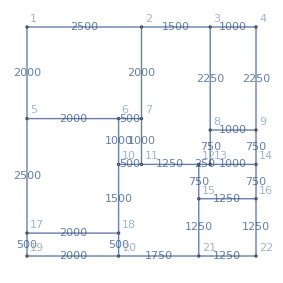

```mathematica
g=Graph[nEdges,VertexLabels->"Name",VertexSize->Medium,EdgeWeight->eWeigth,VertexCoordinates->coord,EdgeLabels->eEdges]
```

Generacion de la lista de poligonos

```mathematica
obtenerListaPoligonos[grafo_,dat_]:=Module[{ g,listaDeVertices,coordenadas,poligonInd,vertice1,vertice2,vertice3,vertice4,coorx1,coorx2,coory1,coory2,
auxiliar,  datos , poligonos},
g=grafo;
datos=dat;
listaDeVertices = VertexList[g];
(*LISTA DE COORDENADAS DE LOS VERTICES DEL GRAFO*)
coordenadas=GraphEmbedding[g];
(*VARIABLES AUXILIARES*)
poligonos={};
vertice1 =0;
(*COORDENADAS DEL VERTICE SUPERIOR IZQUIERDO*)
coorx1=0;
coorx2 =0;
vertice2 =0;
(*COORDENADAS DEL VETICE INFERIOR DERECHO*)
coory1=0;
coory2=0;
vertice3 =0;
vertice4=0;
(*VARIABLE PARA CONSTRUIR EL POLIGONO*)
poligonInd={};
(*AUXILIAR DE VERTICE*)
auxiliar=0;

(*SE RECORREN LAS FILAS DEL ARCHIVO IMPORTADO SALTANDO LA FILA 1*)
For[i=2, i<Length[datos], i++,
(*LA VARIABLE DEL POLIGONO SE LIMPIA*)
poligonInd={};
(*SE DIVIDE EL PROCESO EN DOS, PARA CADA VERTICE EN LA FILA(CADA FILA TIENE 2 VERTICES)*)
For[j=1, j≤ 2, j++,
(*SI ES EL PRIMER CICLO, SE PROCESA EL PRIMER VERTICE*)
If[j==  1,
(*SE OBTIENE EL VERTICE DEL GRAFO QUE CORRESPONDA CON LAS COORDENADAS DADAS EN EL ARCHIVO IMPORTADO*)
vertice1 =Position[coordenadas,{datos[[i]][[1]],datos[[i]][[2]]}][[1]][[1]];
(*SE GUARDAN LAS COORDENADAS DEL VERTICE*)
coorx1 =datos[[i]][[1]];
coory1= datos[[i]][[2]];
,
(*SI ES EL SEGUNDO CICLO, SE PROCESA EL SEGUNDO VERTIDE DE LA FILA DEL ARCHIVO IMPORTADO*)
(*SE GUARDA EL VERTICE*)
vertice2=Position[coordenadas,{datos[[i]][[3]],datos[[i]][[4]]}][[1]][[1]];
(*SE GUARDAN LAS COORDENADAS DEL SEGUNDO EVRTICE*)
coorx2 = datos[[i]][[3]];
coory2= datos[[i]][[4]];
];

];
(*UNA VEZ SE TIENEN LOS VERTICES Y SUS RESPECTIVAS COORDENADAS...*)
(*SE CALCULAN LOS OTROS VERTICES DEL RECTANGULO CON LA MEZCLA DE LAS COORDENADAS DE LOS VERTICES ANTERIORES*)
vertice3 = Position[coordenadas,{coorx1,coory2}][[1]][[1]];
vertice4 = Position[coordenadas,{coorx2,coory1}][[1]][[1]];


(*SE PROCESA EL RECTANGULO PARA ENCONTRAR VERTICES INTERMEDIOS QUE FORMAN PARTE DEL POLIGONO*)
(*EL PROCESO SE REALIZA EN SENTIDO CONTRARIO A LAS MANECILLAS DEL RELOJ, INICIANDO CON EL VERTICE 1, SEGUIDO DEL 3, DEL 4 Y DEL 2*)
(*OBTENER LAS CONEXIONES INTERMEDIAS DE LA HORIZONTAL IZQUIERDA*)
auxiliar = vertice1;
(*SE RECORREN LAS COORDENADAS DE LOS VERTICES DEL GRAFO*)
For[k =1, k≤Length[coordenadas],k++,
(*SI HORIZONTALMENTE SE ENCUENTRA EN LA POSICION DEL PRIMER VERTICE, SE VERIFICA QUE ESTE ENTRE EL VERTICE 1 Y 3*)
If[coordenadas[[k]][[1]]==  coorx1 &&  coordenadas[[k]][[2]]< coory1 && coordenadas[[k]][[2]]>coory2,
(*SE CONECTA ESTE VERTICE CON EL ANTERIOR Y SE AGREGA A LA VARIABLE POLIGONO*)
AppendTo[poligonInd,auxiliar<->k ];
(*EL AUXILIAR SE CONVIERTE EN EL ULTIMO VERTICE*)
auxiliar = k;
]
];
(*SE CONECTA EL ULTIMO VERTICE CON EL VERTICE 3*)
AppendTo[poligonInd,auxiliar<->vertice3];



(*EL PROCESO ANTERIOR SE REPITE EN LOS LADOS RESTANTES*)
(*OBTENER LAS CONEXIONES INTERMEDIAS DE LA VERTICAL INFERIOR*)
auxiliar = vertice3;
For[k =1, k≤Length[coordenadas],k++,
If[coordenadas[[k]][[2]]==  coory2 &&  coordenadas[[k]][[1]]> coorx1 && coordenadas[[k]][[1]]<coorx2,
AppendTo[poligonInd,auxiliar<->k ];
auxiliar = k;
]
];
AppendTo[poligonInd,auxiliar<->vertice2];

(*OBTENER LAS CONEXIONES INTERMEDIAS DE LA HORIZONTAL DERECHA*)
auxiliar = vertice2;
For[k =1, k≤Length[coordenadas],k++,
If[coordenadas[[k]][[1]]==  coorx2 &&  coordenadas[[k]][[2]]< coory1 && coordenadas[[k]][[2]]>coory2,
AppendTo[poligonInd,auxiliar<->k ];
auxiliar = k;
]
];
AppendTo[poligonInd,auxiliar<->vertice4];

(*OBTENER LAS CONEXIONES INTERMEDIAS DE LA VERTICAL SUPERIOR*)
auxiliar = vertice4;
For[k =1, k≤Length[coordenadas],k++,
If[coordenadas[[k]][[2]]==  coory1 &&  coordenadas[[k]][[1]]> coorx1 && coordenadas[[k]][[1]]<coorx2,
AppendTo[poligonInd,auxiliar<->k ];
auxiliar = k;
]
];
AppendTo[poligonInd,auxiliar<->vertice1];
AppendTo[poligonos,poligonInd];
];
(*LA VARIABLE FINAL CONTIENE LA LISTA DE LOS POLIGONOS*)
poligonos

]
```

Obtencion de la lista de vertices en la periferia

```mathematica
getListOfPeriferia[v_]:= Module[{vertices,xs,ys,maxX,maxY,verticesPeriferia},
vertices=v;
(*COORDENADAS DE X*)
xs={};
(*COORDENADAS DE Y*)
ys={};
For[x=1,x≤Length[vertices],x++,
AppendTo[xs,vertices[[x]][[1]] ];
AppendTo[ys,vertices[[x]][[2]] ]
];

(*OBTENER LAS COORDENADAS MAYOYES DEL GRAFO; PARA CONOCER LOS LIMITES*)
(*OBTENCION DE LA COORDENADA EN X MAYOR*)
maxX = Max[xs];
(*OBTENCION DE LA COORDENADA EN Y MAYOR*)
maxY = Max[ys];

(*VARIABLE CONTENEDORA DE LOS VERTICES QUE SE ENCUENTREN EN LA PERIFERIA*)
verticesPeriferia= {};
(*SE RECORRE LA LISTA DE VERTICES Y SUS COORDENADAS*)
For[x=1, x≤Length[vertices],x++,
(*SI LA COORDENADA X O Y SE ENCUENTRA EN LOS LÍMITES DEL GRAFO, ES UN VERTICE EN LA PERIFERIA*)
If[vertices[[x]][[1]]== maxX || vertices[[x]][[2]]== maxY || vertices[[x]][[2]]== 0 || vertices[[x]][[1]]== 0 ,
(*SE AGREGA EL VERTICE A LA LISTA DE VERTICES EN LA PERIFERIA*)
AppendTo[verticesPeriferia, vertices[[x]][[3]] ]
];
];
(*VERTICES DE LA PERIFERIA*)
verticesPeriferia
]
```

Obtener los polígonos de la periferia

```mathematica
poligonosPeriferia[p_,v_]:=Module[{poligonos,vertices,poligonosPeriferia},
poligonos=p;
vertices=v;
poligonosPeriferia= {};
For[i=0, i≤Length[vertices],i++,
For[j=0,j≤Length[poligonos],j++,
If[MemberQ[poligonos[[j]], vertices[[i]]  ],
If[MemberQ[poligonosPeriferia,poligonos[[j]]],
,
AppendTo[poligonosPeriferia,poligonos[[j]]]
];
];
];
];
poligonosPeriferia
]
```

Algoritmo para la obtencion de la ruta más corta

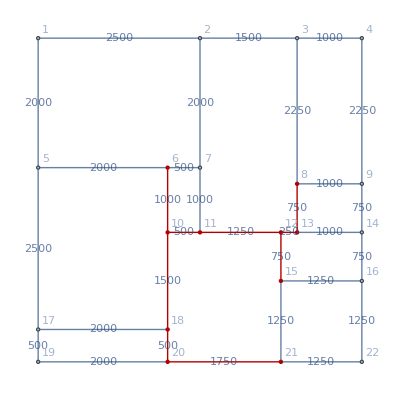

Distancia total mínima:

6500.

Árbol solución:

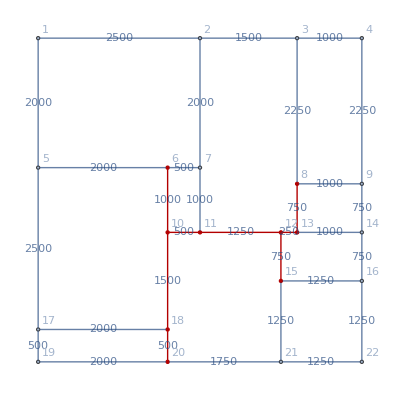

```mathematica
perif = poligonosPeriferia[verticesEnPoligonos,verticesPeriferia];
 grafosSolucion={};

(*NO UTILIZABLE*)

(*SE SELECCIONA EL PRIMERO DE LOS POLIGONOS CUYO VERTICE ESTE EN LA PERIFERIA PARA ANALIZARLO*)
(*SE RECORRE LA LISTA DE POLIGONOS*)
For[i = 1, i≤ Length[verticesEnPoligonos],i++,
(*SE RECORREN LOS VERTICES DEL POLIGONO*)
For[j=0, j≤Length[verticesEnPoligonos[[i]]],j++,
If[MemberQ[verticesPeriferia,verticesEnPoligonos[[i]][[j]] ],
(*SI EL VERTICE ES DE LA PERIFERIA SE SELEECIONA Y SE SALE DEL CICLO*)
poligonoSeleccionado = verticesEnPoligonos[[i]];
Break[]
]
]
]



(*OBTENER LA LISTA DE LOS POLIGONOS EN EL GRAFO*)
Poligonos=obtenerListaPoligonos(g,datos);
(*OBTENER LA LISTA DE LOS VERTICES DE LA PERIFERIA*)
verticesPeriferia = getListOfPeriferia[vertices];


(*OBTENER LOS VERTICES QUE COMPONEN A LOS POLIGONOS*)
verticesEnPoligonos ={};


For[x=1, x≤ Length[Poligonos], x++,
AppendTo[verticesEnPoligonos, VertexList[Poligonos[[x]]] ]
]
(*VARIABLE QUE CONTIENE LOS VERTICES DE CADA POLIGONO*)
verticesEnPoligonos;





Distancias={};


For[m=1, m≤Length[perif],m++,

g=Graph[nEdges,VertexLabels->"Name",VertexSize->Medium,EdgeWeight->eWeigth,VertexCoordinates->coord,EdgeLabels->eEdges];

(*VARIABLES BANDERAS PARA OBTENER EL VERTICE CON MAYORES CONEXIONES*)
vertice =0;
cantidadConexiones =0;
contador =0;
(*LISTA DE VERTICES COMPARTIDOS*)
verticesCompartidos = {};


poligonoSeleccionado=perif[[m]];
(*SE OBTIENE LA LISTA DE LOS POLIGONOS COMO AUXILIAR*)
listaDePoligonos = verticesEnPoligonos;
verticesConMasConexiones = {};


(*OBTENER EL VERTICE CON MAYORES CONEXIONES*)
For[x=1, x≤Length[poligonoSeleccionado], x++,
(*SE VERIFICA QUE SEA UN VERTICE DE LA PERIFERIA*)
If[MemberQ[verticesPeriferia,poligonoSeleccionado[[x]]],
contador =0;
(*SE CUENTA CON CUANTOS VERTICES TIENE CONEXION*)
For[i=1, i≤ Length[verticesEnPoligonos],i++,
If[MemberQ[verticesEnPoligonos[[i]],poligonoSeleccionado[[x]]  ],
contador= contador +1;
];
]
(*SI LA CANTIDAD DE CONEXIONES ES MAYOR A LA BANDERA, SE REMPLAZAN LOS VALORES DE LAS BANDERAS*)
If[contador>cantidadConexiones,
cantidadConexiones = contador;
]
]
];

For[x=1, x≤Length[poligonoSeleccionado], x++,
(*SE VERIFICA QUE SEA UN VERTICE DE LA PERIFERIA*)
If[MemberQ[verticesPeriferia,poligonoSeleccionado[[x]]],
contador =0;
(*SE CUENTA CON CUANTOS VERTICES TIENE CONEXION*)
For[i=1, i≤ Length[verticesEnPoligonos],i++,
If[MemberQ[verticesEnPoligonos[[i]],poligonoSeleccionado[[x]]  ],
contador= contador +1;
];
]
(*SI LA CANTIDAD DE CONEXIONES ES IGUAL A LA CANTIDAD MÁXIMA DE CONEXIONES DEL VERTICE OBTENIDO ANTERIORMENTE*);
If[contador==cantidadConexiones,
(*SE AGREGA EL VERTICE A LA LISTA*)
AppendTo[verticesConMasConexiones,poligonoSeleccionado[[x]]];
]
]
];


(*SE REPITE EL CICLO PARA CADA UNO DE LOS VERTICES*)
For[h=1, h≤Length[verticesConMasConexiones],h++,
(*SE SELECCIONA AL VERTICE CORRESPONDIENTE*)
vertice=verticesConMasConexiones[[h]];
(*SE AGREGA A LA LISTA DE VERTICES COMPARTIDOS*)
AppendTo[verticesCompartidos,vertice];



(*ELIMINAR LOS POLIGONOS QUE COMPARTEN EL VERTICE*)
For[i=1, i≤ Length[listaDePoligonos],i++,
If[MemberQ[listaDePoligonos[[i]],vertice],
listaDePoligonos=Delete[listaDePoligonos,i];
i = i-1;
]
];

(*CICLO*);
While[Length[listaDePoligonos]!=0,
(*OBTENER EL VERTICE CON MÁS CONEXIONES*)
vertice =0;
cantidadConexiones =0;
(*SE CUENTA CON CUANTOS VERTICES TIENE CONEXION*)
For[x=1, x≤Length[poligonoSeleccionado], x++,
contador =0;
(*SE CUENTA CON CUANTOS VERTICES TIENE CONEXION*)
For[i=1, i≤ Length[listaDePoligonos],i++,
If[MemberQ[listaDePoligonos[[i]],poligonoSeleccionado[[x]]  ],
contador= contador +1;
];
(*SI LA CANTIDAD DE CONEXIONES ES MAYOR A LA BANDERA, SE REMPLAZAN LOS VALORES DE LAS BANDERAS*)
If[contador>cantidadConexiones,
cantidadConexiones = contador;
vertice = poligonoSeleccionado[[x]];
]
];
];
(*SI EL POLIGONO YA NO COMPARTE CONEXION CON NINGUNO EN LA LISTA*)
If[contador == 0,
(*RECORRER LOS POLIGONOS*)
For[i=1, i≤Length[listaDePoligonos],i++,
(*RECORRER LOS VERTICES DE LOS POLIGONOS*)
For[j=1, j≤Length[listaDePoligonos[[i]]],j++,
(*UNA VEZ SE TIENE EL VERTICE, SE COMPARA CON TODOS LOS POLIGONOS*)
contador = 0;
For[k=1, k≤Length[verticesEnPoligonos],k++,
(*RECORRER LOS VERTICES DE LOS POLIGONOS*)
If[listaDePoligonos[[i]]≠ verticesEnPoligonos[[k]],
(*SI EL VERTICE TIENE CONEXION CON ALGUN OTRO POLIGONO*)
If[MemberQ[verticesEnPoligonos[[k]],listaDePoligonos[[i]][[j]]  ],
contador= contador +1;
];
];
(*SI LA CANTIDAD DE CONEXIONES ES MAYOR A LA BANDERA, SE REMPLAZAN LOS VALORES DE LAS BANDERAS*)
If[contador>cantidadConexiones,
cantidadConexiones = contador;
vertice = listaDePoligonos[[i]][[j]];
];
];
]
];
];

AppendTo[verticesCompartidos,vertice];
(*ELIMINAR LOS POLIGONOS QUE CONTIENEN EL VERTICE SELECCINADO*)
For[i=1, i≤ Length[listaDePoligonos],i++,
If[MemberQ[listaDePoligonos[[i]],vertice],
listaDePoligonos=Delete[listaDePoligonos,i];
i = i-1;
];
];
 ];
(*LISTA DE VERTICES COMPARTIDOS FINAL*)
(*verticesCompartidos*)
(*VARIABLE QUE CONTENDRÁ LAS RUTAS CORTAS*)
caminocorto={};
(*RECORRER LA LISTA DE LOS VERTICES PARA ENCONTRAR LA RUTA CORTA ENTRE ELLOS*)
For[i=1, i<Length[verticesCompartidos],i++,
(*AGREGAR LAS RUTAS A LA VARIABLE DE CAMINO MAS CORTO*)
AppendTo[caminocorto,FindShortestPath[g,verticesCompartidos[[i]],verticesCompartidos[[i+1]],Method->"Dijkstra"]];
(*HIGLIGHT LA RUTA HECHA EN EL GRAFO*)
g=HighlightGraph[g,PathGraph[caminocorto[[i]]]];
]
(*IMPRIMIR EL CAMINO MÁS CORTO ENTRE LOS VERTICES SELECCIONADOS*)
(*Print["CAMINO ENTRE LOS VERTICES"];*)
caminocorto;
(*MOSTRAR EL GRAFO Y EL CAMINO ENCONTRADO*)


listaDelCamino={};
(*SE OBTIENE UNA LISTA DE LOS VERTICES POR LOS QUE EL CAMINO PASA, RECORRIENDO LA LISTA DE LOS CAMINOS OBTENIDOS POR LA CONEXION CON DJIKSTRA*)
For[i=1,i≤Length[caminocorto],i++,
For[j=1,j≤Length[caminocorto[[i]]],j++,
If[i==1,
(*SE AGREGA EL PRIMER ELEMENTO DE LA SUBLISTA 1*)
AppendTo[listaDelCamino,caminocorto[[i]][[j]]  ];
,
If[j==1,
,
(*A PARTIR DE LA LISTA 2, SE IGNORA EL PRIMER ELEMENTO*)
(*ESTO ES DEBIDO A QUE EL ULTIMO ELEMENTO DE LA LISTA UNO ES EL PRIMER ELEMENTO DE LA SUBLISTA 2, ETC*)
AppendTo[listaDelCamino,caminocorto[[i]][[j]]  ];
];
];
];
];
(*SE INICIALIZA LA VARIABLE DE LA DISTANCIA TOTAL RECORRIDA*)
distancia =0;

(*SE ANALIZA LA LISTA DE LOS VERTICES POR LOS QUE EL CAMINO PASA*)
For[i=1,i<Length[listaDelCamino],i++,
(*LA BANDERA SERVIRA PARA SABER SI SE HA MEDIDO YA EL CAMINO QUE SE ESTÁ ANALIZANDO*)
flag =True;
For[j=1,j<i, j++,
(*CADA PAR DE ELEMENTOS DE LA LISTA SE COMPARA CON LOS PARES DE ELEMENTOS ANTERIORES A ESTOS*)
If[(listaDelCamino[[i+1]]==listaDelCamino[[j]] && 
listaDelCamino[[i]]==listaDelCamino[[j+1]]) || 
(listaDelCamino[[i+1]]==listaDelCamino[[j+1]] &&
listaDelCamino[[i]]==listaDelCamino[[j]])
,
(*SE HA ENCONTRADO UNA SIMILITUD CON LOS PARES, POR TANTO ESTE CAMINO YA SE HA MEDIDO, SE CAMBIA LA BANDERA*)
flag = False;
];
];
(*SI LA BANDERA NO HA CAMBIADO SE MIDE LA DISTANCIA ENTRE LOS VERTICES Y SE SUMAN A LA DISTANCIA DEL RECORRIDO*)
If[flag,
distancia = distancia + GraphDistance[g,listaDelCamino[[i]],listaDelCamino[[i+1]]];
];
];
(*AL FINAL DEL CICLO, SE AGREGA LA DISTANCIA A UNA LISTA DE DISTANCIAS POR CAMINO, Y EL GRAFO SOLUCION A LA LISTA DE GRAFOS SOLUCION*)
AppendTo[Distancias,distancia];
AppendTo[grafosSolucion,g];


];

];
(*LISTA DE LAS DISTANCIAS RECORRIDAS DE CADA ARBOL DE EXPANSION*)
Distancias;
(*LISTA DE LOS GRAFOS CON LOS ARBOLES DE EXPANSION MINIMA ENCONTRADOS*)
grafosSolucion;
(*POSICION DEL ELMENTO MAS PEQUEÑO DE LAS DISTANCIAS DE LOS ARBOLES DE EXPANSION*)
position = Position[Distancias,Min[Distancias]][[1]];
Print["Distancia total mínima:"]
Distancias[[position]][[1]]
Print["Árbol solución:"]
(*ARBOL SOLUCION QUE REPRESENTA AL ARBOL DE EXPANSION MINIMA DE ENTRE LOS PROCESADOS*)
Solucion=grafosSolucion[[position]][[1]]
```